```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/Moat-meanfield/MF_DR/renorm_finitep_v2/specfun/T50/mu200

```mathematica
Re1=Import["./Redata.dat"];
Im1=Import["./Imdata.dat"];
omega=Table[i,{i,1,2001,10}];
ϵ=0.5;
Re2=Re1;
Im2=Table[{Im1[[i]][[j]]-2ϵ omega[[j]]},{i,1,201},{j,1,201}];
spec=-1/π*Im2/(Re2^2+Im2^2);
```

```mathematica
ListPlot3D[spec,PlotRange->{All,All,{0,0.000001}}]
```

ListPlot3D::gmat: {{7.93548×10^-10,8.83791×10^-9,1.74465×10^-8,2.72286×10^-8,3.90067×10^-8,5.40116×10^-8,«40»,1.66768×10^-9,1.48864×10^-9,1.32813×10^-9,1.18378×10^-9,«151»}} 不是一个大于 2 x 2 的矩形数组.

```mathematica
special=Clip[spec,{0,0.0000015}];
```

```mathematica
ListPlot3D[special]
```

-Graphics3D-

```mathematica
Export["spec.dat",special]
```

spec.dat

```mathematica
ListPlot3D[Re1]
```

-Graphics3D-

```mathematica
ListPlot3D[-Im1]
```

-Graphics3D-

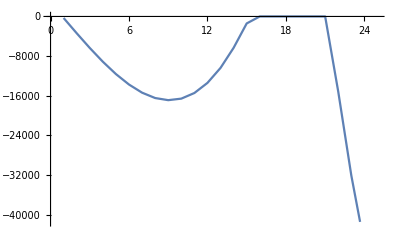

```mathematica
ListLinePlot[Im1[[30]][[1;;25]]]
```